# When should genomic imprinting affect sexual maturation?

```mathematica
Clear["Global`*"]
```

## Parameters

```mathematica
tdip={tff->1/2,tmf->1/2,tfm->1/2,tmm->1/2};
thapdip={tff->1/2,tmf->1,tfm->1/2,tmm->0};
```

Fecundity and survival functions:

```mathematica
ϕ[a_]:=(k a)^3
σ[a_]:=Exp[-μ a]
```

## Fitness expressions a_f

```mathematica
wff=1/2 tff f[afi](((1-df)s[afji])/(f[afff](1-df)s[afjff]+f[af]df s[af])+(df s[afji])/(f[af]s[af]));
```

```mathematica
wmf=1/2 tmf f[afi]((nm(1-dm))/(nf(f[afff](1-dm)+f[af]dm))+(nm dm)/(nf f[af]));
wfm=1/2 tfm nf/nm(l f[affm](((1-df)s[afji])/(f[affm](1-df)s[afjfm]+f[af]df s[af])+(df s[afji])/(f[af]s[af]))+(1-l)s[afjinonloc]/s[af]);
wmm=1/2 tmm nf/nm(l f[affm]((nm(1-dm))/(nf(f[affm](1-dm)+f[af]dm))+(nm dm)/(nf f[af]))+(1-l)nm/nf);
```

## Fitness expressions a_m

```mathematica
wamff=1/2 tff ;
```

```mathematica
wammf=1/2 tmf ((nm(1-dm)s[amji])/(nf((1-dm)s[amjmf]+dm s[am]))+(nm dm s[amji])/(nf s[am]));
wamfm=1/2 tfm nf/nm(l f[ami]/(l f[ammm]+(1-l)f[am])+(1-l)f[ami]/f[am]);
wammm=1/2 tmm nf/nm(l f[ami]/(l f[ammm]+(1-l)f[am])((nm(1-dm)s[amji])/(nf((1-dm)s[amjmm]+dm s[am]))+(nm dm s[amji])/(nf s[am]))+(1-l)(nm f[ami]s[amjinonloc])/(nf f[am]s[am]));
```

## Reproductive values, class frequencies

Demographical model of homogeneous population

```mathematica
A={{wff,wfm},{wmf,wmm}}/.{affm->af,afff->af,afjfm->af,afjff->af,afji->af,afi->af,afjinonloc->af,amjinonloc->am}//Simplify
```

{{tff/2,(nf tfm)/(2 nm)},{(nm tmf)/(2 nf),tmm/2}}

```mathematica
evals=Simplify[Eigenvalues[A]]
```

{1/4 (tff+tmm-√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)),1/4 (tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2))}

```mathematica
classfreqs=Simplify[Eigenvectors[1/evals[[2]] A]]
```

{{-(nf (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1},{(nf (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1}}

```mathematica
repvals=Simplify[Eigenvectors[1/evals[[2]] Transpose[A]]]
```

{{-(nm (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1},{(nm (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1}}

### Diplodiploidy

Stable class frequencies

```mathematica
udipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.tdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
udip={uf->udipR[[1]],um->udipR[[2]]};
```

Individual reproductive values

```mathematica
vdipR=Simplify[repvals[[2]]/Total[udipR.repvals[[2]]]/.tdip]
```

{(nf+nm)/(2 nf),(nf+nm)/(2 nm)}

```mathematica
vdip={vf->vdipR[[1]],vm->vdipR[[2]]};
```

Class reproductive values

```mathematica
cdip={cf->vf uf,cm->vm um}/.vdip/.udip
```

{cf→1/2,cm→1/2}

### Haplodiploidy

```mathematica
uhapdipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.thapdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
uhapdip={uf->uhapdipR[[1]],um->uhapdipR[[2]]};
```

Individual reproductive values

```mathematica
vhapdipR=Simplify[repvals[[2]]/Total[uhapdipR.repvals[[2]]]/.thapdip]
```

{(2 (nf+nm))/(3 nf),(nf+nm)/(3 nm)}

```mathematica
vhapdip={vf->vhapdipR[[1]],vm->vhapdipR[[2]]};
```

Class reproductive values

```mathematica
chapdip={cf->vf uf,cm->vm um}/.vhapdip/.uhapdip
```

{cf→2/3,cm→1/3}

## Selection gradient on a_f

```mathematica
Wfaf=wff+vm/vf wmf;
Wmaf=wmm+vf/vm wfm;
```

```mathematica
selgradaf=cf(D[Wfaf,afi]rfi+D[Wfaf,afji]rfkidf+D[Wfaf,afff]rff+D[Wfaf,afjff]rflocjf)+cm(D[Wmaf,afji]rmkidf+D[Wmaf,afjinonloc]rmkidfnonloc+D[Wmaf,affm]rmf+D[Wmaf,afjfm]rmlocjf)/.{afi->af,afji->af,afjinonloc->af,afff->af,afjff->af,affm->af,afjfm->af}//Simplify
```

1/(2 nf nm vf vm f[af] s[af])(-(cf nm vm (nf ((-1+df)^2 rff-rfi) tff vf+nm ((-1+dm)^2 rff-rfi) tmf vm)+cm l nf rmf vf (-2 df nf tfm vf+df^2 nf tfm vf+(-2+dm) dm nm tmm vm)) s[af] f'[af]+nf vf (cm nf (rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) tfm vf+cf nm (rfkidf-(-1+df)^2 rflocjf) tff vm) f[af] s'[af])

## Selection gradient on a_m

```mathematica
Wfam=wamff+vm/vf wammf;
Wmam=wammm+vf/vm wamfm;
```

```mathematica
Wfam//Variables
```

{tff,tmf,vf,vm,dm,nf,nm,s[am],s[amji],s[amjmf]}

```mathematica
selgradam=cf(D[Wfam,amji]rfkidm+D[Wfam,amjmf]rflocjm)+cm(D[Wmam,ami]rmi+D[Wmam,amji]rmkidm+D[Wmam,amjinonloc]rmkidmnonloc+D[Wmam,ammm]rmm+D[Wmam,amjmm]rmlocjm)/.{amji->am,amjmf->am,ami->am,ammm->am,amjmm->am,amjinonloc->am}//Simplify
```

1/(2 nf nm vf vm f[am] s[am])(cm nf (rmi-l^2 rmm) vf (nf tfm vf+nm tmm vm) s[am] f'[am]-nm vm (cm nf (-rmkidmnonloc+l (-rmkidm+rmkidmnonloc+(-1+dm)^2 rmlocjm)) tmm vf+cf nm (-rfkidm+(-1+dm)^2 rflocjm) tmf vm) f[am] s'[am])

## Relatedness

### Diplodiploidy

#### Coefficients of consanguinity

```mathematica
hf=1-df;
hm=1-dm;
```

```mathematica
Qdip={QffJ==QmmJ==QfmJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
Qf==1/2(1+l Qfm),
Qf==Qm,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsoldip=Solve[Qdip,{QffJ,QmmJ,QfmJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rdip={
rfi->Qf,
rmi->Qm,
rfkidm->1/2(1+l Qfm),
rfkidf->1/2(1+l Qfm),
rmkidf->1/2(1+Qfm),
rmkidm->1/2(1+Qfm),
rmkidfnonloc->1/2,
rmkidmnonloc->1/2,
rff->1/nf Qf+(nf-1)/nf Qff,
rmf->Qmf,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmlocjf->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf
}/.Qsoldip;
```

Expression by mother (M)

```mathematica
rdipM={
rfi->1/2(Qf+l Qfm),
rmi->1/2(Qf+l Qfm),
rfkidm->1/2(1+Qf),
rfkidf->1/2(1+Qf),
rmkidf->Qfm,
rmkidm->Qfm,
rmkidfnonloc->0,
rmkidmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+(nf-1)/nf(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rmf->1/2(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rmm->1/2 1/nm(Qf+l Qfm)+(nm-1)/nm(1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/2 1/nf(1+Qf)+(nf-1)/nf Qff,
rflocjm->1/2 1/nf(1+Qf)+(nf-1)/nf Qff,
rmlocjf->Qfm,
rmlocjm->Qfm
}/.Qsoldip;
```

Expression by father (P)

```mathematica
rdipP={
rfi->1/2(Qm+l Qfm),
rmi->1/2(Qm+l Qfm),
rfkidf->l Qfm,
rfkidm->l Qfm,
rmkidfnonloc->1/2(1+Qm),
rmkidmnonloc->1/2(1+Qm),
rmkidm->1/2(1+Qm),
rmkidf->1/2(1+Qm),
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rmf->1/2 l 1/nm(Qm+ Qfm)+1/2(nm-1)/nm l (l Qmm +Qfm),
rmm->1/2 1/nm(Qm+l Qfm)+1/2(nm-1)/nm(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l 1/2 1/nm(1+Qm)+l 1/2(nm-1)/nm Qmm,
rmlocjm->l 1/2 1/nm(1+Qm)+l 1/2(nm-1)/nm Qmm
}/.Qsoldip;
```

Expression by maternally-inherited alleles (MI)

```mathematica
rdipMI={
rfi->Qf,
rmi->Qm,
rfkidf->1,
rfkidm->1,
rmkidf->Qfm,
rmkidm->Qfm,
rmkidfnonloc->0,
rmkidmnonloc->0,
rff->1/nf Qf+1/2(nf-1)/nf(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmf->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmm->1/nm Qf+1/2(nm-1)/nm(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rflocjf->1/nf 1+(nf-1)/nf Qff,
rflocjm->1/nf 1+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsoldip;
```

```mathematica
rdipPI={
rfi->Qf,
rmi->Qm,
rfkidf->l Qfm,
rfkidm->l Qfm,
rmkidf->1,
rmkidm->1,
rmkidfnonloc->1,
rmkidmnonloc->1,
rff->1/nf Qm+1/2(nf-1)/nf(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rfm->1/2 l 1/nm(Qm+Qfm)+1/2(nm-1)/nm l (l Qmm+Qfm),
rmf->1/2 l 1/nm(Qm+Qfm)+1/2(nm-1)/nm l (l Qmm+Qfm),
rmm->1/nm Qm+1/2(nm-1)/nm(1/nm l(Qm+Qfm)+(nm-1)/nm l(l Qmm+Qfm)),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l(1/nm+(nm-1)/nm Qmm),
rmlocjm->l(1/nm+(nm-1)/nm Qmm)}/.Qsoldip;
```

### Haplodiploidy

#### Coefficients of consanguinity haplodiploidy

```mathematica
Qhapdip={QffJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
QfmJ==QmfJ==1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
QmmJ==1/nf Qf+(nf-1)/nf Qff,
Qf==1/2(1+l Qfm),
Qm==1,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsolhapdip=Solve[Qhapdip,{QffJ,QmmJ,QfmJ,QmfJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients haplodiploidy

Expression of alleles in offspring

```mathematica
rhapdip={
rfi->Qf,
rmi->Qm,
rfkidf->Qf,
rfkidm->Qm,
rmkidf->Qf,
rmkidm->Qfm,
rff->1/nf Qf+(nf-1)/nf Qff,
rfm->Qmf,
rmf->Qmf,
rmkidfnonloc->1/2,
rmkidmnonloc->0,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by mother (M)

```mathematica
rhapdipM={
rfi->1/2(Qf+l Qfm),
rmi->Qf,
rfkidf->1/2(1+Qf),
rfkidm->1/2(1+Qf),
rmkidf->Qfm,
rmkidm->Qfm,
rmkidfnonloc->0,
rmkidmnonloc->0,
rff->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(1/nf(Qf+l Qfm)+(nf-1)/nf(Qff+l Qfm)),
rfm->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmf->1/nf Qf+1/2(nf-1)/nf Qff,
rmm->1/nm Qf+(nm-1)/nm(1/nf Qf+(nf-1)/nf Qff),
rflocjf->1/2 1/nf(1+Qf)+(nf-1)/nf Qff,
rflocjm->1/2 1/nf(1+Qf)+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by father (P)

```mathematica
rhapdipP={
rfi->1/2(Qm+l Qfm),
rmi->Qm,
rfkidf->l Qfm,
rfkidm->Qm,
rmkidf->1,
rmkidm->Qfm,
rmkidfnonloc->Qm,
rmkidmnonloc->0,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf(1/nm(Qm+l Qfm)+(nm-1)/nm l (l Qmm+Qfm)),
rfm->Qmf,
rmf->l Qmf,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm+(nm-1)/nm Qmm),
rmlocjm->Qmf
}/.Qsolhapdip;
```

```mathematica
rhapdipMI={
rfi->Qf,
rmi->Qm,
rfkidf->1,
rfkidm->1,
rmkidf->Qfm,
rmkidm->Qfm,
rmkidfnonloc->0,
rmkidmnonloc->0,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rfm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmf->1/nf Qf+(nf-1)/nf Qff,
rmm->1/nm+(nm-1)/nm Qmm,
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsolhapdip;
```

```mathematica
rhapdipPI={
rfi->Qf,
rmi->Qm,
rfkidf->l Qfm,
rfkidm->Qm,
rmkidf->1,
rmkidm->Qfm,
rmkidfnonloc->Qm,
rmkidmnonloc->0,
rff->1/2 1/nf(1+Qfm)+1/2(nf-1)/nf l(Qfm+l Qmm),
rmf->Qmf,
rfm->Qfm,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf}/.Qsolhapdip;
```

## Analytical results diplodiploidy

```mathematica
afamsol=Solve[{selgradaf==0,selgradam==0},{s'[af],s'[am]}]/.vdip/.cdip/.{tff->1/2,tfm->1/2,tmf->1/2,tmm->1/2}//FullSimplify//Flatten
```

{s'[af]→(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) f[af]),s'[am]→-(2 (rmi-l^2 rmm) s[am] f'[am])/((rfkidm-(-1+dm)^2 rflocjm+rmkidmnonloc+l (rmkidm-rmkidmnonloc-(-1+dm)^2 rmlocjm)) f[am])}

```mathematica
rfcoeff={rfselfjuvf->rfkidf+l rmkidf+(1-l)rmkidfnonloc,
rfcompetingjuvf->hf^2(rflocjf+l rmlocjf),
rfownoffspring->rfi+l rmf,
rfcompetingoffspring->1/2(hf^2+hm^2)(rff+l rmf)
};
rmcoeff={rmselfjuvm->l rmkidm+rfkidm+(1-l)rmkidmnonloc,
rmcompetingjuvm->hm^2(rflocjm+l rmlocjm),
rmownoffspring->rmi,
rmcompetingoffspring->l rmm};
```

Check algebra s’[af]

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)
```

(2 (rfi+l rmf-1/2 ((1-df)^2+(1-dm)^2) (rff+l rmf)) s[af] f'[af])/((-rfkidf-l rmkidf-(1-l) rmkidfnonloc+(1-df)^2 (rflocjf+l rmlocjf)) f[af])

```mathematica
s'[af]/.afamsol//Simplify
```

(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidfnonloc+l (rmkidf-rmkidfnonloc-(-1+df)^2 rmlocjf)) f[af])

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)==(s'[af]/.afamsol)//FullSimplify
```

True

Check algebra s’[am]

```mathematica
(((rmownoffspring-rmcompetingoffspring)s[am])/(-1/2(rmselfjuvm-rmcompetingjuvm))f'[am]/f[am]/.rmcoeff)==(s'[am]/.afamsol)//Simplify
```

((-1+l) l rmm s[am] f'[am])/((rfkidm-(-1+dm)^2 rflocjm+l rmkidm+rmkidmnonloc-l rmkidmnonloc-l rmlocjm+2 dm l rmlocjm-dm^2 l rmlocjm) f[am])==0

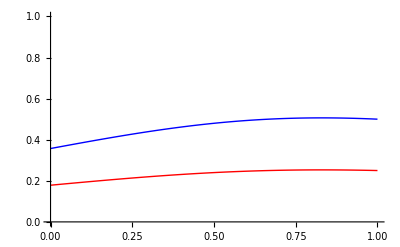

```mathematica
Plot[{.5(rmselfjuvm-rmcompetingjuvm)/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rmownoffspring-rmcompetingoffspring/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm}},
{dm,0,1},PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1}}]
```

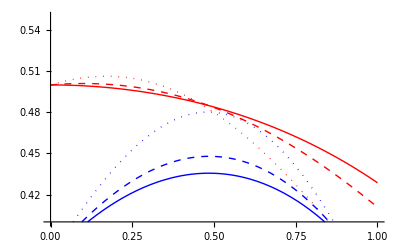

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm}
},
{dm,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Red},{Blue,Dotted},{Blue,Dashed},{Blue}},PlotRange->{{0,1},{0.4,.55}}]
```

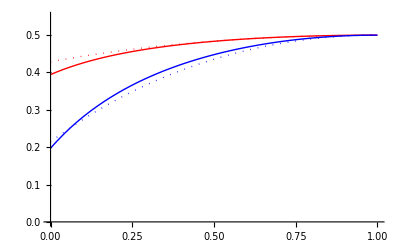

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

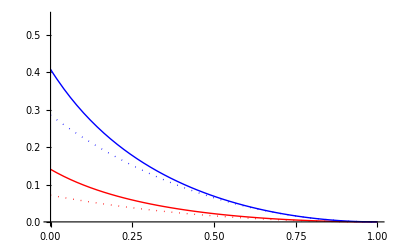

```mathematica
Plot[{.5rfcompetingjuvf/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5 rfcompetingjuvf/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

## Results diplodiploidy

```mathematica
ans[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdip/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipMI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipPI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipM/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipP/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansPI[{2,2},{0.5,0.9,1},{1,1/3}]
```

{af→3.9203,am→1.1197}

### Figure 1

```mathematica
a1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a2=Table[{{dm,af},{dm,am}}/.ansM[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a3=Table[{{dm,af},{dm,am}}/.ansP[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a4=Table[{{dm,af},{dm,am}}/.ansMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a5=Table[{{dm,af},{dm,am}}/.ansPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
```

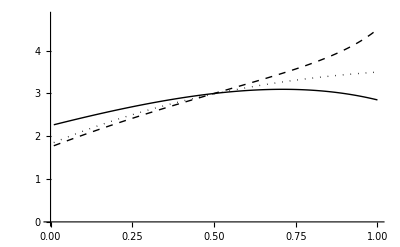

```mathematica
plotbattle1=ListLinePlot[{Transpose[a1][[1]],Transpose[a2][[1]],Transpose[a3][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

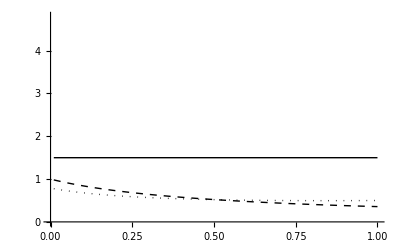

```mathematica
plotbattle1m=ListLinePlot[{Transpose[a1][[2]],Transpose[a2][[2]],Transpose[a3][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

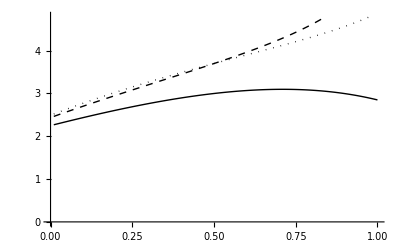

```mathematica
plotbattle2=ListLinePlot[{Transpose[a1][[1]],Transpose[a4][[1]],Transpose[a5][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

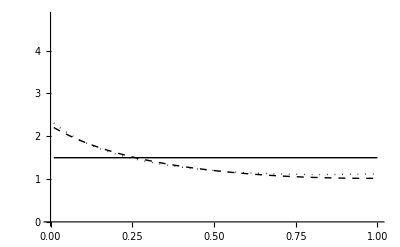

```mathematica
plotbattle2m=ListLinePlot[{Transpose[a1][[2]],Transpose[a4][[2]],Transpose[a5][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

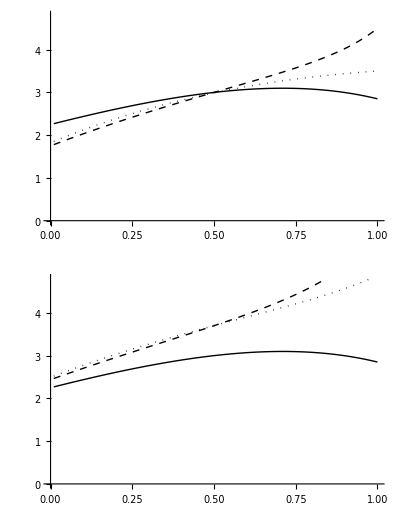
-Graphics-Sex-biased dispersal, d_m=1-d_fFemale age at maturity, a_f

```mathematica
plotaf=Labeled[GraphicsGrid[{{plotbattle1},{plotbattle2}}],{"Sex-biased dispersal, d_m=1-d_f","Female age at maturity, a_f"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

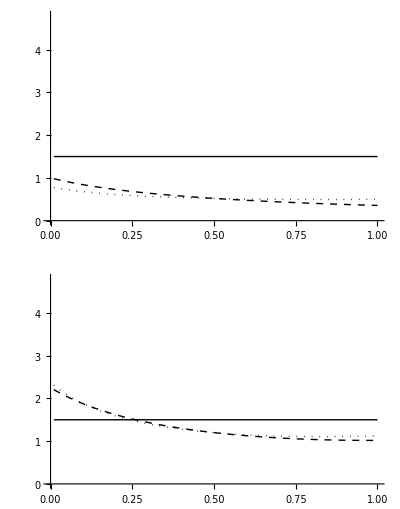
-Graphics-Sex-biased dispersal, d_m=1-d_fMale age at maturity, a_m

```mathematica
plotam=Labeled[GraphicsGrid[{{plotbattle1m},{plotbattle2m}}],{"Sex-biased dispersal, d_m=1-d_f","Male age at maturity, a_m"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

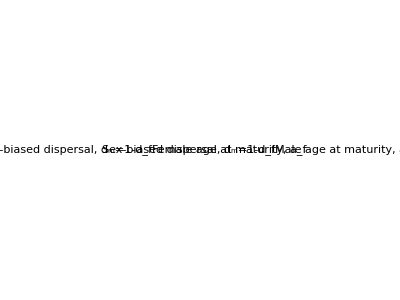

```mathematica
plotafam=GraphicsGrid[{{plotaf,plotam}}]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/battleground.pdf",plotafam]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/battleground.pdf

## Results haplodiploidy

```mathematica
anshap[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdip/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipM/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipP/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipMI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipPI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{4,4},{0.9,0.1,0.5},{1,1/3}]
```

{af→2.70062,am→2.97534}

### Figure S1

```mathematica
a1hap=Table[{{dm,af},{dm,am}}/.anshap[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a2hap=Table[{{dm,af},{dm,am}}/.anshapM[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a3hap=Table[{{dm,af},{dm,am}}/.anshapP[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a4hap=Table[{{dm,af},{dm,am}}/.anshapMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a5hap=Table[{{dm,af},{dm,am}}/.anshapPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
```

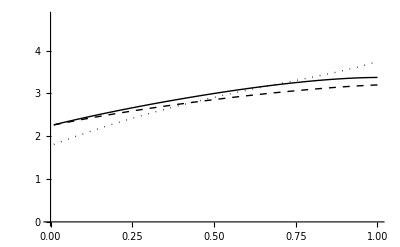

```mathematica
plotbattle1=ListLinePlot[{Transpose[a1hap][[1]],Transpose[a2hap][[1]],Transpose[a3hap][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

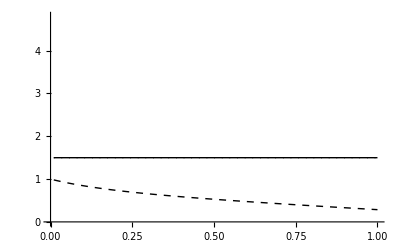

```mathematica
plotbattle1m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a2hap][[2]],Transpose[a3hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed},{Black,Dotted}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

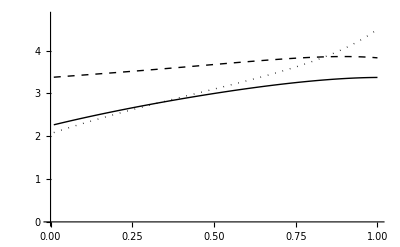

```mathematica
plotbattle2=ListLinePlot[{Transpose[a1hap][[1]],Transpose[a4hap][[1]],Transpose[a5hap][[1]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

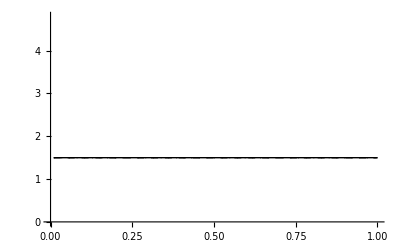

```mathematica
plotbattle2m=ListLinePlot[{Transpose[a1hap][[2]],Transpose[a4hap][[2]],Transpose[a5hap][[2]]},PlotStyle->{{Black,Normal},{Black,Dashed,Thick},{Black,Dotted,Thick}},PlotRange->{{0,1},{0,4.8}},BaseStyle->{FontFamily->"Helvetica"}]
```

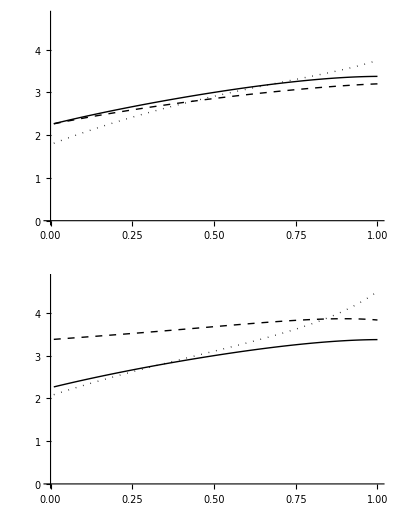
-Graphics-Sex-biased dispersal, d_m=1-d_fFemale age at maturity, a_f

```mathematica
plotaf=Labeled[GraphicsGrid[{{plotbattle1},{plotbattle2}}],{"Sex-biased dispersal, d_m=1-d_f","Female age at maturity, a_f"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

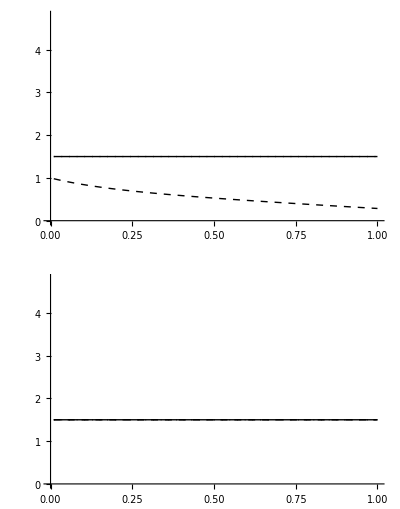
-Graphics-Sex-biased dispersal, d_m=1-d_fMale age at maturity, a_m

```mathematica
plotam=Labeled[GraphicsGrid[{{plotbattle1m},{plotbattle2m}}],{"Sex-biased dispersal, d_m=1-d_f","Male age at maturity, a_m"},{Bottom,Left},RotateLabel->True,LabelStyle->{FontFamily->"Helvetica"}]
```

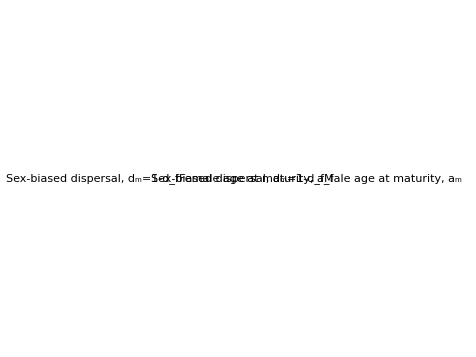

```mathematica
plotafam=GraphicsGrid[{{plotaf,plotam}}]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf",plotafam,ImageSize->{475,250}]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/battleground_haplodiploid.pdf

## Export to C

```mathematica
rlistdip={{"dip",rdip},{"dipM",rdipM},{"dipP",rdipP},{"dipMI",rdipMI},{"dipPI",rdipPI}};
rlisthapdip={{"hapdip",rhapdip},{"hapdipM",rhapdipM},{"hapdipP",rhapdipP},{"hapdipMI",rhapdipMI},{"hapdipPI",rhapdipPI}};
```

```mathematica
str="";
For[iter=1,iter≤Length[rlistdip],iter++,
str=str<>"af"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlistdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlistdip[[iter,2]]/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
For[iter=1,iter≤Length[rlisthapdip],iter++,
str=str<>"af"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradaf/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
str=str<>"am"<>rlisthapdip[[iter,1]]<>"<-expression("<>ToString[CForm[selgradam/.rlisthapdip[[iter,2]]/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}]]<>")\n\n";
]
```

```mathematica
Export[$HomeDirectory<>"/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions.txt",str]
```

/home/bram/Projects/age_vs_size_imprint/figs/effect_phil/mathematica_expressions.txt